```mathematica
<<MaTeX`
SetOptions[MaTeX,FontSize->12,Magnification->1,"DisplayStyle"->True]
style=Directive[FontFamily->"LM Roman 12",FontSize->10];
cm=72/2.54;
(* http://ksrowell.com/blog-visualizing-data/2012/02/02/optimal-colors-for-graphs/ *)
col1 = RGBColor[57/256, 106/256, 177/256]
col2 = RGBColor[218/256, 124/256, 48/256]
col3= RGBColor[62/256, 150/256, 81/256]
col4 = RGBColor[204/256, 37/256, 41/256]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

RGBColor[Rational[57, 256], Rational[53, 128], Rational[177, 256]]

RGBColor[Rational[109, 128], Rational[31, 64], Rational[3, 16]]

RGBColor[Rational[31, 128], Rational[75, 128], Rational[81, 256]]

RGBColor[Rational[51, 64], Rational[37, 256], Rational[41, 256]]

## Optimal

Data generated on 2020-03-06 in QDS_Holevo_scans_deltaphi.nb

```mathematica
bs0bestlist ={{0.01,{0.25,0.5,9.142495056876142*^6}},{0.1,{0.26,0.5,828966.8218192516}},{0.2,{0.28,0.5,367456.5068350603}},{0.30000000000000004,{0.3,0.6,213351.5167884158}},{0.4,{0.32,0.6,136225.18472425264}},{0.5,{0.36,0.6,89898.91621634628}},{0.6,{0.41,0.6,59056.19671959349}},{0.7000000000000001,{0.51,0.7,36887.00869828592}},{0.8,{0.8,0.9,20154.27678611152}},{0.9,{0.95,0.8,8207.024057684905}},{0.99,{1.05,0.7,2134.2722847906425}}};
```

```mathematica
bs1bestlist  = {{0.01,{0.24,0.5,8.731757141393326*^6}},{0.1,{0.26,0.5,791597.4058027847}},{0.2,{0.27,0.5,350596.07556367695}},{0.30000000000000004,{0.3,0.6,203507.36651967868}},{0.4,{0.32,0.6,129776.37108177313}},{0.5,{0.35,0.6,85632.46965379873}},{0.6,{0.41,0.6,56109.459023909054}},{0.7000000000000001,{0.51,0.7,35001.254650539944}},{0.8,{0.65,0.7,19142.956268065926}},{0.9,{0.95,0.8,7630.7789189247715}},{0.99,{1.05,0.7,1745.5045741565907}}};
```

```mathematica
bs2bestlist={{0.01,{0.25,0.5,9.169139104805121*^6}},{0.1,{0.26,0.5,831478.7159451011}},{0.2,{0.28,0.5,368660.7796215242}},{0.30000000000000004,{0.3,0.6,214123.33685466327}},{0.4,{0.32,0.6,136756.6786590415}},{0.5,{0.36,0.6,90300.20182603673}},{0.6,{0.41,0.6,59362.94774464935}},{0.7000000000000001,{0.51,0.7,37131.25603108656}},{0.8,{0.8,0.9,20325.300968418353}},{0.9,{0.95,0.8,8290.855458613503}},{0.99,{1.05,0.7,2234.992011605959}}};
```

```mathematica
ecbestlist={{0.01,Null},{0.1,Null},{0.2,{0.5,1.5,2.1073647088166833*^8}},{0.30000000000000004,{0.43,0.9,2.0562582536438077*^6}},{0.4,{0.44,0.8,513910.0957476483}},{0.5,{0.47,0.8,212740.34579390008}},{0.6,{0.51,0.7,104193.10580505064}},{0.7000000000000001,{0.55,0.7,53680.22895023128}},{0.8,{0.8,0.9,24508.08901533409}},{0.9,{0.95,0.8,9622.21038465103}},{0.99,{1.05,0.7,2722.2800573020595}}};
```

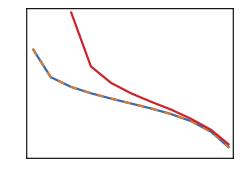

C:\Users\MatthewThornton\OneDrive for Business\Thesis\Writing\Images\qds\QDSf_optimal_L.pdf

```mathematica
fs1=15;
fs2=10;
fig = ListLogPlot[
{
{bs0bestlist[[;;,1]], bs0bestlist[[;;,2,3]]}//Transpose,
{bs2bestlist[[;;,1]], bs2bestlist[[;;,2,3]]}//Transpose,
{ecbestlist[[3;;,1]], ecbestlist[[3;;,2,3]]}//Transpose
},
Joined->True, PlotRange->All,
PlotStyle->{col1, {col2, Dashed}, col4},
ImageSize->8.6cm,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4
,FrameTicks->{{
Join[{
{0.0, MaTeX[ "0.0", ContentPadding->False, FontSize->fs2]},(*{5*10^5,MaTeX[ "5 \\times 10^5", ContentPadding->False, FontSize->fs2]},*)
{1*10^6,MaTeX[ "10^6", ContentPadding->False, FontSize->fs2]},
(*{1.5*10^6,MaTeX[ "1.5 \\times 10^6", ContentPadding->False, FontSize->fs2]}*)
{1*10^5,MaTeX[ " 10^5", ContentPadding->False, FontSize->fs2]},
{1*10^4,MaTeX[ "10^4", ContentPadding->False, FontSize->fs2]},
{1*10^3,MaTeX[ "10^3", ContentPadding->False, FontSize->fs2]},
{1*10^7,MaTeX[ "10^7", ContentPadding->False, FontSize->fs2]},
{1*10^8,MaTeX[ "10^8", ContentPadding->False, FontSize->fs2]},
{1*10^9,MaTeX[ "10^9", ContentPadding->False, FontSize->fs2]}


},Transpose[{Range[9]*10^5,Table[Null, 9]}],
Transpose[{Range[9]*10^4,Table[Null, 9]}],
Transpose[{Range[9]*10^3,Table[Null, 9]}],
Transpose[{Range[9]*10^6,Table[Null, 9]}],
Transpose[{Range[9]*10^7,Table[Null, 9]}],
Transpose[{Range[9]*10^8,Table[Null, 9]}]
]
, None},
{{{0.8, MaTeX["0.80", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]},
{0.6, MaTeX["0.6", ContentPadding->False, FontSize->fs2]},
{0.4, MaTeX["0.4", ContentPadding->False, FontSize->fs2]},
{0.2, MaTeX["0.2", ContentPadding->False, FontSize->fs2]},
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}

},None}},
FrameLabel->{MaTeX["T", ContentPadding->False, FontSize->fs1], MaTeX["L", ContentPadding->False, FontSize->fs1]}
];
fig~Magnify~2
Export["C:\\Users\\MatthewThornton\\OneDrive for Business\\Thesis\\Writing\\Images\\qds\\QDSf_optimal_L.pdf", fig]
```

## Non-optimal

Gotta run initialization cells from QDS_Holevo_scans_deltaphi.nb first

```mathematica
Tlist
```

{0.01,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.99}

```mathematica
bs0nonoptlist[α_, Δr_]:=bs0nonoptlist[α, Δr]=Monitor[Table[
{T, length["BS0", α, T, 0.0, 7, Δr, 0.0]},
{T, Tlist}
],T]
```

```mathematica
ecnonoptlist[α_, Δr_]:=ecnonoptlist[α, Δr]=Monitor[Table[
{T, length["EC", α, T, 0.1/100, 8, Δr, 0.0]},
{T, Tlist}
],T]
```

```mathematica
.
```

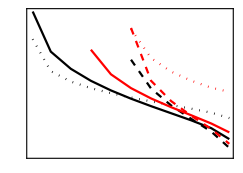

C:\Users\MatthewThornton\OneDrive for Business\Thesis\Writing\Images\qds\QDSf_nonoptimal_L.pdf

```mathematica
fs1=15;
fs2=10;
fig = ListLogPlot[
{
bs0nonoptlist[0.5, 0.0],
bs0nonoptlist[0.8, 0.0],
bs0nonoptlist[0.2, 0.0],
ecnonoptlist[0.5, 0.0],
ecnonoptlist[0.8, 0.0],
ecnonoptlist[0.2, 0.0]
},
Joined->True,
PlotStyle->{Black, {Black, Dashed}, {Black, Dotted}, Red, {Red, Dashed}, {Red, Dotted}},
ImageSize->8.6cm,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4
,FrameTicks->{{
Join[{
{0.0, MaTeX[ "0.0", ContentPadding->False, FontSize->fs2]},(*{5*10^5,MaTeX[ "5 \\times 10^5", ContentPadding->False, FontSize->fs2]},*)
{1*10^6,MaTeX[ "10^6", ContentPadding->False, FontSize->fs2]},
(*{1.5*10^6,MaTeX[ "1.5 \\times 10^6", ContentPadding->False, FontSize->fs2]}*)
{1*10^5,MaTeX[ " 10^5", ContentPadding->False, FontSize->fs2]},
{1*10^4,MaTeX[ "10^4", ContentPadding->False, FontSize->fs2]},
{1*10^3,MaTeX[ "10^3", ContentPadding->False, FontSize->fs2]},
{1*10^7,MaTeX[ "10^7", ContentPadding->False, FontSize->fs2]},
{1*10^8,MaTeX[ "10^8", ContentPadding->False, FontSize->fs2]},
{1*10^9,MaTeX[ "10^9", ContentPadding->False, FontSize->fs2]}


},Transpose[{Range[9]*10^5,Table[Null, 9]}],
Transpose[{Range[9]*10^4,Table[Null, 9]}],
Transpose[{Range[9]*10^3,Table[Null, 9]}],
Transpose[{Range[9]*10^6,Table[Null, 9]}],
Transpose[{Range[9]*10^7,Table[Null, 9]}],
Transpose[{Range[9]*10^8,Table[Null, 9]}]
]
, None},
{{{0.8, MaTeX["0.8", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]},
{0.6, MaTeX["0.6", ContentPadding->False, FontSize->fs2]},
{0.4, MaTeX["0.4", ContentPadding->False, FontSize->fs2]},
{0.2, MaTeX["0.2", ContentPadding->False, FontSize->fs2]},
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}

},None}},
FrameLabel->{MaTeX["T", ContentPadding->False, FontSize->fs1], MaTeX["L", ContentPadding->False, FontSize->fs1]}
];
fig~Magnify~2
Export["C:\\Users\\MatthewThornton\\OneDrive for Business\\Thesis\\Writing\\Images\\qds\\QDSf_nonoptimal_L.pdf", fig]
```